# Ultrafast dynamics driven by femtosecond lasers in Chern insulators: implementation of semiconductor Bloch equation in topological materials A. Chacon

## Semiconductor Bloch Equations (SBEs) to describe the laser-topological-material interaction

(1)     ∂_t π(k⃗,t) - E⃗(t) ·∇ π(k⃗,t)  = -ⅈ[ϵ_g(  k⃗ )   + (ξ⃗)_g(k⃗) · E⃗(t)  - ⅈ/T2]  π(k⃗,t)   -  ⅈ  (d⃗)_cv(k⃗)  ·  E⃗(t);      Evolution of the coherence,  π(k⃗,t)
     (2)     ∂_t n_c(k⃗,t) - E⃗(t) ·∇ n_c(k⃗,t)  = -2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                         Evolution of the Occupation, conduction band, nc
     (3)     ∂_t n_v(k⃗,t) - E⃗(t) ·∇ n_v(k⃗,t)  = +2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                   Evolution of the Occup. of the valence band, nv
       
 Constrain,
        nc(k⃗,t)  + nv(k⃗,t)  =1

```mathematica
ClearAll["Global`*"] ;

Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];

$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`26"&);
efac=27.2;

rootPathA="/Users/achacon/Documents/Workplace/MichaelC/TopologyProj/CodeDeveloping/SF/Mathematica/";(*"/Users/achacon/Documents/Workplace/MichaelC/TopologyProj/CodeDeveloping/March19_2019/";*)

toFixedWidth[n_Integer,width_Integer]:=StringJoin[PadLeft[Characters[ToString[n]],width,"0"]];
toNumberedFileName[fname_,n_Integer]:=ToString@StringForm[fname<>toFixedWidth[n,5]];

NotebookDirectory[];
AbsoluteTime[];
```

```mathematica
qindex0 = 0;
fname0 = toNumberedFileName["BinaryTest",0];
fname0 = toNumberedFileName[fname0<>"_kyIndex_",qindex0];

testList ={-1.01,0,1,2.0001};
file=  rootPathA <> fname0 <> ".bin";
BinaryWrite[file,testList,"Real64"];
BinaryReadList[file,"Real64"];
Close[file];
```

```mathematica
(*Sin2:=Function[x, x - x^3/3/2 +0  x^5/(5!) ]
Cos2:=Function[x,1- x^2 /2+ x^4/(4!)  ]*)

Sin2:=Function[x, Sin[x] ]
Cos2:=Function[x,Cos[x] ]
```

## Laser field

```mathematica
Af :=Function[t, 

e0/w0 (Cos[w0 t] Exp[-.5(t/alpha0)^2] -  Cos[w0 tmin0]  Exp[-.5(tmin0/alpha0)^2])

];

Efa := Function[t, -D[Af[ta],ta]/.ta-> t];
Ef := Function[t, Efa[t]-Efa[tmin0]];

timeaxes := Function[
{dt,Nt},
tmax= dt*(Nt-1)/2.;
wmax=Pi/dt;
dw = 2 Pi/Nt/dt;
{Table[tmin0 + i dt,{i,0,Nt-1}]
,Table[-wmax + i dw,{i,0,Nt-1}]
}
];
```

## Haldane Model (HM) and topological Chern insulators Hamiltonian and its “components” B0, B1,... H(k) = B0*sig0 + B1*sig1 + B2*sig2 + B3*sig3 where, sig1, sig2, sig3 are Pauli’s matrices, sig0 identity matrix

```mathematica
B0 := Function[
{kx,ky}
,2 t2 Cos[ϕ]*
Sum[ 

tempB0= kx *bx[[i]] +ky *by[[i]];

Cos2[tempB0  ] 

,{i,1,3}
] 
];


B1:= Function[
{kx,ky}
, t1 *
Sum[ 
tempB1=kx *ax[[i]] +ky *ay[[i]];
Cos2[ tempB1 ]

,{i,1,3}

]
];


B2:= Function[
{kx,ky} 
, t1 Sum[
 tempB2=kx *ax[[i]] +ky *ay[[i]];
Sin2[ tempB2 ]
,{i,1,3}
]
];


B3 := Function[ 
{kx,ky}
,M-2 t2*Sin[ϕ]Sum[ 
tempB3=kx *bx[[i]] +ky *by[[i]];
Sin2[ tempB3 ]
,{i,1,3} 

] 
];


BNorm:=Function[
{kx,ky}
, Sqrt[ 
B1[kx,ky]^2 +B2[kx,ky]^2+B3[kx,ky]^2
 ]
];


(*Definition of quantize indexes/axes*)
nB1:=Function[
{kx,ky}
, B1[kx,ky]/BNorm[kx,ky] 
];


nB2:=Function[
{kx,ky}
,B2[kx,ky]/BNorm[kx,ky] 
];


nB3:=Function[
{kx,ky}
, B3[kx,ky]/BNorm[kx,ky] 
];
```

## Invariant easy quantities

```mathematica
(*Definition of Energy dispersion for conduction and valance band*)
Ec:=Function[{kx,ky}
, 
B0[kx,ky]  + BNorm[kx,ky]

];



Ev:=Function[{kx,ky}
, B0[kx,ky]  - BNorm[kx,ky]
];



(*Group velocities of the conduction and valance band*)
cGroupVel := Function[{kx,ky}
,Grad[Ec[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky->ky
];



vGroupVel := Function[{kx,ky},
Grad[Ev[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky->ky
];



(*Energy Gap, Eg = Ec- Ev and Berry Connection 'Chig' Gap*)
 Eg := Function[
{kx,ky}
, Ec[kx,ky] 
- Ev[kx,ky] 
];


(*Functions to rotate axis*)
QuantizationAxis:=Function[{kx,ky},
{1,0,0} (*Return vector {1,0,0}*)
]


(*ROTATEING FUNCTION ALONG DIFFERNT SPIN-AXIS "PAULI MATRIXES"*)
RotateOnBAt0:=

Function[{kx,ky},
Module[
{
n3p,n2p,n1p,

nBVecAtK = 
{
    nB1[kx,ky]
,nB2[kx,ky]
,nB3[kx,ky]
},

nB3p,nB2p,nB1p, orthoVecs

},

n3p =QuantizationAxis[kx,ky] ;
orthoVecs =
 Orthogonalize[
{
n3p
,RotateLeft[n3p,1]
,RotateLeft[n3p,2]
}
];

n1p = orthoVecs[[3]];
n2p = orthoVecs[[2]];

nB3p = nBVecAtK.n3p;
nB2p = nBVecAtK.n2p;
nB1p = nBVecAtK.n1p;

{nB1p,nB2p,nB3p}
]
];


RotateUNOnBAt0:=Function[
{kx,ky},

Module[{
n3p,n2p,n1p,orthoVecs,
bVecAtK = 
{
     B1[kx,ky]
, B2[kx,ky]
, B3[kx,ky]
},
b3p,b2p,b1p
},

n3p =QuantizationAxis[kx,ky] ;

orthoVecs = Orthogonalize[
{
n3p
,RotateLeft[n3p,1]
,RotateLeft[n3p,2]
}

];

n1p = orthoVecs[[3]];
n2p = orthoVecs[[2]];

b3p = bVecAtK.n3p;
b2p = bVecAtK.n2p;
b1p = bVecAtK.n1p;

{b1p,b2p,b3p}
]

];
```

## New connections and Berry features

```mathematica
(*singular points at gauge (1,0,0)*)

ks00 ={-1.7,0};
ks01 ={-1.7+2 kxMax,0};

ks10 ={0.8,1.45};
ks11 ={0.8-2 kxMax,1.45};
ks12 ={0.8,-1.45};
ks13 ={0.8-2 kxMax,-1.45};

ks20 ={-1.1,1.85};
ks21 ={-1.1+2 kxMax,1.85};
ks22 ={-1.1,-1.85};
ks23 ={-1.1+2 kxMax,-1.85};


MyRegularization := Function[{kx,ky,ks},

reg0 Exp[-((ky-ks[[2]])^2+(kx-ks[[1]])^2)/width]

]

QuantizationAxis:=Function[
{kx,ky},
{1,0,0}
]


Hamilton:= Function[{kx,ky},
Module[
{

B0p = B0[kx,ky],
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]

(*B1p=B1[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by],
B2p=B2[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by],
B3p=B3[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]*)

},

B0p IdentityMatrix[2] + B1p PauliMatrix[1] +B2p PauliMatrix[2] + B3p PauliMatrix[3]

]

];

HamiltonGrad := Function[{kx,ky},

Grad[Hamilton[kkx,kky],{kkx,kky}]/.kkx-> kx/.kky-> ky

];


ANorm:= Function[{kx,ky},

Module[
{
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
},
(*
temp=2Sqrt[2]/2 (BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] + B3p/2 - 1/8 B3p^2/BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] + 0/16 B3p^3/BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]^2 );

Sqrt[
  2( B1p^2 +B2p^2+B3p^2) +  
2 BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] *0];
*)


Sqrt[
  2( B1p^2 +B2p^2+B3p^2) +  
2 BNorm[kx,ky] B3p
]



(*

Sqrt[
  2( B1p^2 +B2p^2+B3p^2) +  
2 BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] B3p
]+MyRegularization[kx,ky,ks00]+ MyRegularization[kx,ky,ks01]
+MyRegularization[kx,ky,ks10]+MyRegularization[kx,ky,ks11]
+MyRegularization[kx,ky,ks12]+MyRegularization[kx,ky,ks13]
+MyRegularization[kx,ky,ks20]+MyRegularization[kx,ky,ks21]
+MyRegularization[kx,ky,ks22]+MyRegularization[kx,ky,ks23]

*)
]


];


uCondNew:=Function[{kx,ky}
,
Module[
{
B1p =RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
},

{
B3p +  BNorm[kx,ky]
,
B1p + I B2p
}/ANorm[kx,ky]
]
];


uValNew:=Function[
{kx,ky}

,Module[
{
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
}
,{
-B1p + I B2p,
+B3p +  BNorm[kx,ky]

}/ANorm[kx,ky]
]
	
];


VWaveGrad := Function[

{kx,ky}

,Grad[uValNew[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky-> ky


];


CWaveGrad := Function[
{kx,ky}

,Grad[uCondNew[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky-> ky

];


(*BERRY CONNECTION FOR THE CONDUCTION BAND*)
cBerryConnection := Function[{kx,ky},

BCon=Re[I Conjugate[uCondNew[kx,ky]]. CWaveGrad[kx,ky]];


BCon

];


(*DIPOLE MATRIX ELEMENT BETWEEN THE VALENCE AND CONDUCTION BAND*)
cvDipole := Function[

{kx,ky},

I Conjugate[uCondNew[kx,ky]]. VWaveGrad[kx,ky]

(*If[ky<0,tempDip=-tempDip ];*)

(*tempDip*)

];


vcDipole := Function[
{kx,ky},

I Conjugate[uValNew[kx,ky]]. CWaveGrad[kx,ky]

];

(*BERRY CURVATURE FOR THE CONDUCTION BAND*)
cBerryCurvature:= Function[

{kx,ky},

Re[I  (
Conjugate[CWaveGrad[kx,ky][[All,1]]].CWaveGrad[kx,ky][[All,2]]
- Conjugate[CWaveGrad[kx,ky][[All,2]]].CWaveGrad[kx,ky][[All,1]]
)]

];


cBerryCurvaDipole := Function[{kx,ky},
2 Im[ 
Conjugate[cvDipole[kx,ky][[1]] ] cvDipole[kx,ky][[2]]  
]
]




(********************************)
(*Calculation of the CHERN No.*)

CherNo[t1_,t2_,M_,ϕ_,ax_,ay_,bx_,by_]:=
 NIntegrate[cBerryCurvature[kx,ky],{kx,kxMin,kxMax},{ky,
kyMin, kyMax}  ]/(2 Pi)/2
```

## Axis and finite difference derivative under periodic boundary conditions

```mathematica
(* Momentum axis *)
momaxis := Function[
{Nk,kmin},

dk=-2kmin/(Nk-1);
Table[kmin + dk i,{i,0,Nk-1}]

]; 

(*Derivative operator*)
FirstDerOperator := Function [
{dx,Nx},

Mtemp=SparseArray[{Band[{1,1}]->0,Band[{2,1}]->-1,Band[{1,2}]->1},{Nx,Nx}]/2/dx;
Mtemp[[1]][[Nx-1]]=1/dx/2.;
Mtemp[[Nx]][[2]]=-1/dx/2.;
Mtemp

];



MM=  FirstDerOperator[1/2,4];(*{{-1,1,0,0},{-1,0,1,0},{0,-1,0,1},{0,0,-1,1}};*)
vect0={m0,m1,m2,m3};
MM.vect0
```

{m1+1. m2,-m0+m2,-m1+m3,-1. m1-m2}

## Vector bases of HM (Hexagonal lattice)

```mathematica
(*Lattice Constant*)
a0=1.0/0.529;(*4.5/0.529*)


(*Next Nearest Neighbor, NNN, vectors of the HoneyComb Lattice*)
b1 = {Sqrt[3],0}*a0;
b2 = {-Sqrt[3]/2,+3/2}*a0;
b3 = {-Sqrt[3]/2,-3/2}*a0;

bx1=b1[[1]];
by1=b1[[2]];

bx2=b2[[1]];
by2=b2[[2]];

bx3=b3[[1]];
by3=b3[[2]];

b = {b1,b2,b3};


(*Nearest Neighbor, NN, vectors of the HoneyComb Lattice*)
a1 = {0,1}*a0;
a2 = {-Sqrt[3]/2,-1/2}*a0;
a3 = {Sqrt[3]/2,-1/2}*a0;

a= {a1,a2,a3};


ax1=a1[[1]];
ay1=a1[[2]];

ax2=a2[[1]];
ay2=a2[[2]];

ax3=a3[[1]];
ay3=a3[[2]];

aax ={ a1[[1]],a2[[1]],a3[[1]] };
aay ={ a1[[2]],a2[[2]],a3[[2]] };

bbx ={ b1[[1]],b2[[1]],b3[[1]] };
bby ={ b1[[2]],b2[[2]],b3[[2]] };

(*Creating momentum axis limits*)
xtemp=   N[ Pi/Sqrt[3]/a0];
ytemp=   N[2 Pi/3/a0];
kxMin= - xtemp ; kxMax=xtemp;
kyMin = - ytemp  ; kyMax=ytemp ; 


(*K' and K points with respect to the gamma points on the BZ*)
K1= {-4 Pi/(3*Sqrt[3] a0),0};
K2 = {4 Pi/(3*Sqrt[3] a0),0};

t1=0.075;
t2=t1/3;
M=2.54* t2;
phi0=1.16; 
ϕ=0.06;

t01=0.075;
t02=t01/3;
M0=2.54* t02;

xdir=1;
ydir=2;

size=450;

ax=aax;
ay=aay;
bx=bbx;
by=bby;
```

```mathematica
gauge={1,0,0};

QuantizationAxis:=Function[
{kx,ky},
gauge
];

eps0=t01/2.;
width =0.1^2;
reg0=0.000001;
vect1=uCondNew[kxMax,0];
vect2=Conjugate[uCondNew[kxMax,0]];
vect2.vect1
vect1//Dimensions
```

1.+0. ⅈ

{2}

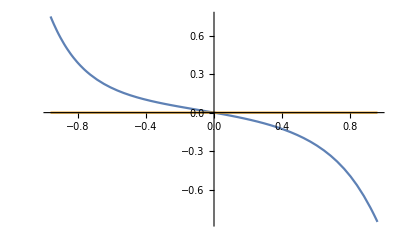

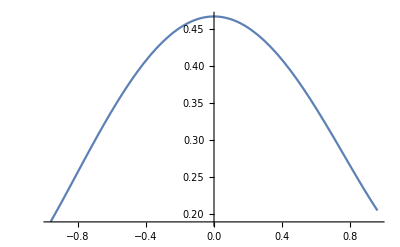

```mathematica
Plot[{Re[cvDipole[kx,0]][[1]],Im[cvDipole[kx,0]][[1]]},{kx,kxMin,kxMax},PlotRange->All]
Plot[Eg[kx,0],{kx,kxMin,kxMax},PlotRange->All]
```

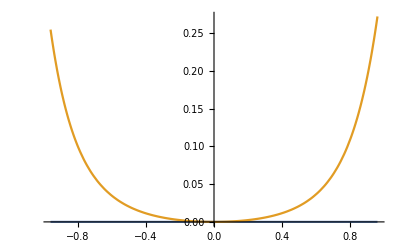

```mathematica
Plot[{cBerryConnection[kx,0][[1]],cBerryConnection[kx,0][[2]]},{kx,kxMin,kxMax},PlotRange->All]
```

## Laser Parameters and HM parameters

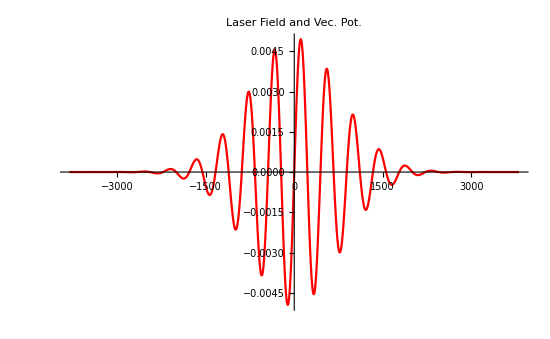

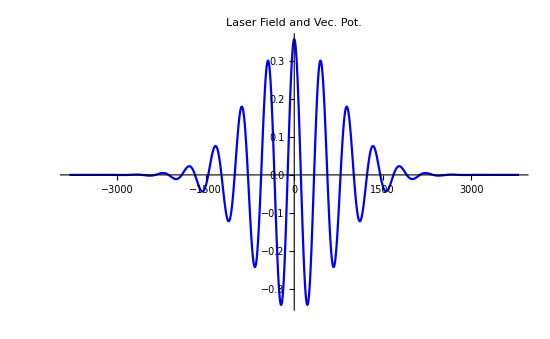

```mathematica
(* Laser parameters *)
w0=0.014; (*laser freq.*)
e0 = 0.005; (*laser field amplitude*)
T0= 2 Pi/w0; (*laser cycle or period*)
Ncycles = 4; (*No. of cycles*)

alpha0 = Ncycles*T0/2.355; (*time width*)
tmax = 5 alpha0;
tmin0=-tmax;
tmin=-tmax;


Plot[{
Ef[t]
}
,{t,tmin0,tmax}
,PlotRange->All,
PlotStyle->{Red}
,ImageSize->550
,PlotLabel->"Laser Field and Vec. Pot."
]

Plot[{
Af[t]
}
,{t,-tmax,tmax}
,PlotRange->All,
PlotStyle->{Blue}
,ImageSize->550
,PlotLabel->"Laser Field and Vec. Pot."
]


regular = 10^-10; (*Regularization of Dipole*)
(* xdirection dir =1, ydirection dir=2 *)
dir = 1;
```

```mathematica
Ef[tmin]
Af[tmin]
```

0.

0.

## Energy Band Gap

```mathematica
(***********************)
(*Max and Min gap*)
dkx1=0.07;
dky1=0.07;

phi0=0.4;
(*M0=0.035;
t01=0.02;
t02=t01/3.;*)

Tac = Table[Ec[kx,ky]
,{kx,kxMin,kxMax,dkx1}
,{ky,kyMin,kyMax,dky1}
];

Tav = Table[Ev[kx,ky]
,{kx,kxMin,kxMax,dkx1}
,{ky,kyMin,kyMax,dky1}
];

(*Print["\n\nM/t2 = ",M0/t02,";  t2/t1 = ",t02/t01, ";\nt1= ",t01*efac, " eV; t2= ",t02*efac," eV;\nM= ",M0*efac," eV; phi0= ",phi0, " rad."]
Print["\nBand-Gap= ",Min[Tac-Tav]*efac,";   Max Gap=", Max[Tac-Tav]*efac," eV",";  phi0 = ",N[phi0,4], ";  C = ",N[CherNo[t01,t02,M0,phi0,aax,aay,bbx,bby],4]]*)

N1=2;
Table[

phi0=Pi/N1/2. i;
ϕ=Pi/N1/2. i;

Tav = Table[Eg[kx,ky]
,{kx,kxMin,kxMax,dkx1}
,{ky,kyMin,kyMax,dky1}
];

Eg0=Min[Tav];
cn0=CherNo[t01,t02,M0,ϕ,aax,aay,bbx,bby]2;

{phi0,
Eg0* efac,
cn0
}
,{i,0,N1}]//TableForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

0 | 3.45619 | 6.09143×10^-17
0.062831853071795864769252868 | 3.01284 | -6.35783×10^-15
0.12566370614359172953850574 | 2.57133 | -2.37781×10^-15
0.1884955592153875943077586 | 2.13346 | -1.47491×10^-14
0.25132741228718345907701147 | 1.70105 | -3.41333×10^-14
0.31415926535897932384626434 | 1.27606 | -3.55186×10^-14
0.37699111843077518861551721 | 0.860831 | 7.64834×10^-14+0. ⅈ
0.43982297150257105338477007 | 0.459946 | -1.8044×10^-13
0.50265482457436691815402294 | 0.122366 | -1.98981×10^-12
0.56548667764616278292327581 | 0.349418 | -1.
0.62831853071795864769252868 | 0.707115 | -1.
0.69115038378975451246178154 | 1.05489 | -1.
0.75398223686155037723103441 | 1.3864 | -1.
0.81681408993334624200028728 | 1.69941 | -1.
0.87964594300514210676954015 | 1.99238 | -1.
0.94247779607693797153879301 | 2.26404 | -1.
1.0053096491487338363080459 | 2.51324 | -1.
1.0681415022205297010772988 | 2.73896 | -1.
1.1309733552923255658465516 | 2.9403 | -1.
1.1938052083641214306158045 | 3.11645 | -1.
1.2566370614359172953850574 | 3.24862 | -1.
1.3194689145077131601543102 | 3.31051 | -1.
1.3823007675795090249235631 | 3.35159 | -1.
1.445132620651304889692816 | 3.38175 | -1.
1.5079644737231007544620688 | 3.3977 | -1.
1.5707963267948966192313217 | 3.40251 | -1.

```mathematica
-Cross[{Ex,Ey,0},{0,0,Ωz}]
```

{-Ey Ωz,Ex Ωz,0}

## Chern Number

```mathematica
(********************************)
(*Calculation of the CHERN No.*)

reg0=0 .00000000075;
ϕ=1.16;
M=2.54 t2;
width=0.;
CherNo[t1,t2,M,ϕ,ax,ay,bx,by] 2
```

1.

## Time Axis and more parameters

```mathematica
(* Laser parameters *)
w0=0.014; (*laser freq.*)
e0 = 0.005; (*laser field amplitude*)


T0= 2. Pi/w0; (*laser cycle or period*)
dt=2.;(*T00/160.06/2*) (*Time step*)


Ncycles = 4.; (*No. of cycles*)
alpha0 = Ncycles*T0/(2.*Sqrt[2.*Log[2.]]); (*time width or integration window*)
tmax = 5. alpha0;
tmin=-tmax;
tmin0=-tmax;
Ntime = Floor[2 tmax/dt]-1;

Print["\ndt = ",N[dt,4], "\nNtime = ",Ntime,"\n"];


(*Numerical time axis for time evolution of SBEs*)
tme= timeaxes[dt,Ntime];
time=tme[[]][[1]];
freq = tme[[]][[2]]; 
time[[1]]
T2 = 220; (*Dephasing*)

(* some Momentum parameters *)
xdir = 1;
ydir=2;
kxMax0 = kxMax; (*Max grid space momentum *)
```

dt = 2.
Ntime = 3810

-3811.747326169283090895371

# Momentum axis and derivative operator

```mathematica
(*Momentum Axis*)
Nkx= 11; (*30*)

kxx = momaxis[Nkx,kxMin]; (*momentum space axis*)
dkx = kxx[[2]]-kxx[[1]];(*2 kxMax/(Nkx-1); *)(*Momentum space step => momentum step*)
kxx0=kxx;

(*Rabbi Freq. *)
ROmega := Function[

{kx,ky,t}

,Ef[t]*
cvDipole[ kx, ky][[xdir]] 

];

ConjROmega := Function[

{kx,ky,t}

,Ef[t]*Conjugate[ cvDipole[ kx, ky][[xdir]] ]

];


(*Stability condition*)
CFL=e0 dt/dkx ;
Print["\nCFL = ",CFL];


MaskFunc := Function[{t,ta,tb,al,om,dat },
Ntime=Length[t];

Table[

taux=t[[j]];

If[taux≤ ta, 

Exp[-2(taux-ta)^2 /(al*al)]*dat[[j]]
,

If[taux≤  tb,
dat[[j]],
Exp[-2(taux-tb)^2 /(om*om)]*dat[[j]]
]

]

,{j,1,Ntime}
]

];
```

CFL = 0.0521105

```mathematica
dt
```

2

## Dynamical evolution of populations and SBEs defined by Eqs 1 -- 3, according to the constriction

```mathematica
Fehlbergamat={{1/4},{3/32,9/32},{1932/2197,-7200/2197,7296/2197},{439/216,-8,3680/513,-845/4104},{-8/27,2,-3544/2565,1859/4104,-11/40}};Fehlbergbvec={25/216,0,1408/2565,2197/4104,-1/5,0};Fehlbergcvec={1/4,3/8,12/13,1,1/2};Fehlbergevec={-1/360,0,128/4275,2197/75240,-1/50,-2/55};FehlbergCoefficients[4,p_]:=N[{Fehlbergamat,Fehlbergbvec,Fehlbergcvec,Fehlbergevec},p];


DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Clear[solver,t];
(*ϕ=0.06;*)
gauge={1,0,0};
QuantizationAxis:=Function[
{kx,ky},
gauge
];
ϕ=0.06;
solver=

(*NDSolve[*)
ParametricNDSolve[
{

(*******************************************)
(****     Evol. Equations of SBEs       ****)
(*******************************************)
(*Equation1*)
D[pi[t],t]  == 
-I(
 Eg[kx+Af[t],ky] 

+2. Ef[t] * cBerryConnection[kx+Af[t],ky][[xdir]]

-  I/T2
)* pi[t] 

- I *ROmega[kx+Af[t],ky,t] *(1. - 2.*nc[t])



(*Equation2*)
,D[nc[t],t] == -2*Im[ ConjROmega[kx+Af[t],ky,t]* pi[t] ]
(*******************************************)


(*******************************************)
(****             Initials             ****)
(*******************************************)
(*Initials1*)
(*,pi[kxMin,t]==pi[kxMax,t]*)
,pi[tmin]==0.

(*Initials2*)
(*,nc[kxMin,t]==nc[kxMax,t]*)
,nc[tmin]==0.
(*******************************************)

}

,{pi,nc}

(*,{kx,kxMin,kxMax}*)

,{t,tmin,tmax}

(*,Method->"ImplicitRungeKutta",*)
(*,Method-> RK5*)

,{kx,ky}
,AccuracyGoal->10,PrecisionGoal->10

,MaxStepSize->{dt}
                            
          ,Method->{"ExplicitRungeKutta"
,"DifferenceOrder"->5
,"Coefficients"->DOPRICoefficients
(*,"StiffnessTest"->False*)}

];
```

```mathematica
ktime=1+0Ntime/2;
kx1=kxMin
ky1=0;
Re[         

 Evaluate[         nc[kx1,ky1][    time[[ktime]]    ]/.solver     ]   
   
]
```

-0.9595

-2.03916×10^-55

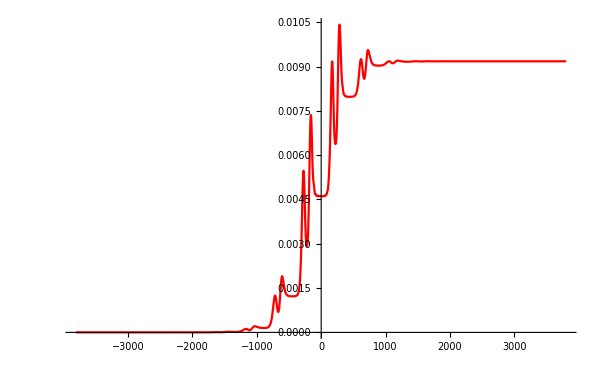

```mathematica
ncSol=Table[ 
kx1=kxMin;
ky1=0;
{time[[ktime]],Re[Evaluate[nc[kx1,ky1][time[[ktime]]]/.solver]]}
,{ktime,0,Ntime}
];
ListLinePlot[ncSol,PlotRange->All, ImageSize->600,PlotStyle->Red]
```

```mathematica
(*InterDipole Radiation x-direction*)
InterDipole := Function[
{vcdip,pcoh}, 
vcdip.pcoh
];


(*InterDipole Radiation y-direction*)


(*Exact Density of Group velocity, x-dir*)
groupVelocity := Function[
{vvel0,cvel0,anc},

nc00=anc;
nv0     =1.-nc00;


nv0.vvel0 + nc00.cvel0

];



(*Anomalous velocity operator omn y-dir*)
anomalousVelCB := Function[
{t,vBCurva0,cBCurva0,anc},
anv0     =1.-anc;

- Ef[t]*(anc.cBCurva0+anv0.vBCurva0)

];


Der2nd:=Function[{vec,dt,Ntime},

res=Table[

If[ i>1 &&i<Ntime,

(vec[[i+1]]-vec[[i-1]])/2./dt,

,
0. *dt]

,{i,1,Ntime}];

res[[1]]=0.;
res[[Ntime]]=0.;

res

]
```

## Numerical evaluation of Mathematica solutions

```mathematica
phi0=0.06;
Print["Gauge = ",gauge];

Nky=10;
Nkx=11;
ist=1;
dky=kyMax/Nky;

Print["\nNkx = ",Nkx, ";    dkx = ",dkx];
Print["\nNky = ",Nky, ";    dky = ",dky];

Do[

time01=AbsoluteTime[];
(*kxx=kxx0+kxMax;*)

(*yshift = kyMin+dky *kyindex ;*)
yshift=0;
Nsnaper=1;

(*If[yshift > -.15, 

gauge={1,0,0};

QuantizationAxis:=Function[
{kx,ky},
gauge
];

];*)

Print["\nkyIndex = ",kyindex, ";     ky = ", yshift, ";       Gauge = ", gauge];


pi1 = Table[

itemp=i;
kxtemp=kxx[[itemp]];

Evaluate[ 

pi[   kxtemp,yshift ][   time[[j*Nsnaper]]  ]/.solver 

] 

,{i,ist,Nkx}

,{j,1,Ntime/Nsnaper}

];


nc1 = Table[
itemp=i;
kxtemp=kxx[[itemp]];

Re[      
Evaluate[   
 nc[ kxtemp, yshift ][    time[[j*Nsnaper]]     ]/.solver    
]    
 ] 

,{i,ist,Nkx}

,{j,1,Ntime/Nsnaper}

];


xvcdip = Table[ 

itemp=i;
xktemp=kxx[[itemp]];

Conjugate[ cvDipole[ xktemp, yshift][[xdir]]  ]

,{i,ist,Nkx}

];

yvcdip = Table[ 

itemp=i;
xktemp=kxx[[itemp]];

Conjugate[ cvDipole[ xktemp, yshift][[ydir]]   ]

,{i,ist,Nkx}
];
	
xvvel0= Table[ 

itemp=i;
xktemp=kxx[[itemp]];
 
vGroupVel[xktemp,yshift][[xdir]]

,{i,ist,Nkx}

];

xcvel0= Table[ 

itemp=i;
xktemp=kxx[[itemp]];

cGroupVel[xktemp,yshift][[xdir]]

,{i,ist,Nkx}

];

yvvel0= Table[ 

itemp=i;
xktemp=kxx[[itemp]];

 vGroupVel[xktemp,yshift][[ydir]]

,{i,ist,Nkx}

];

ycvel0= Table[ 

itemp=i;
xktemp=kxx[[itemp]];

cGroupVel[xktemp,yshift][[ydir]]

,{i,ist,Nkx}

];



cBCurva0 =  Table[ 
itemp=i;
xktemp=kxx[[itemp]];

Re[cBerryCurvature[xktemp,yshift]]

,{i,ist,Nkx}

];

vBCurva0 =  -cBCurva0;


(*************************************************
x-direction analysis for the inter-band current
   ****)
DtimeOp = FirstDerOperator[dt,Ntime];

xInterRad0 = Table[


xvcdip = Table[ 

itemp=i;
xktemp=kxx[[itemp]]+Af[ time[[j]] ];

Conjugate[ cvDipole[ xktemp, yshift][[xdir]]  ]

,{i,ist,Nkx}

];

(*2*Re[ InterDipole[xvcdip, pi1[[j,All]] ] ]*dkx*)
Sum[ 
2 Re[
xvcdip[[i]] * pi1[[i]][[j]]
]
,
{i,ist,Nkx}]*dkx

,{j,1,Ntime}

];


(*Momentum expectation value of the dipole moment on x-direction*)
xDipoleMom = xInterRad0;

(******************************)
(*x-Interband Current*)

(*xInterRad=DtimeOp.xDipoleMom;*)
xInterRad=Der2nd[xDipoleMom,dt,Ntime];

(******************************)


(*************************************************
y-direction analysis for the inter-band current
    ****)
yInterRad0 = Table[


Sum[
2. Re[     yvcdip[[i]]* pi1[[i]][[j]]      ] 
,{i,ist,Nkx} 
] *dkx

,{j,1,Ntime}

];


(*Momentum expectation value of the dipole moment on y-direction*)
yDipoleMom = yInterRad0;

(******************************)
(*y-Interband Current*)

(*yInterRad=DtimeOp.yDipoleMom;*)
yInterRad=Der2nd[yDipoleMom,dt,Ntime];

(*xInterRad0=xInterRad;
yInterRad0=yInterRad;

ta0=-(Ncycles) T00*1.12;
tb0=(Ncycles) T00*1.12;

xInterRad=MaskFunc[time,ta0,tb0,T00,T00,xInterRad];
yInterRad=MaskFunc[time,ta0,tb0,T00,T00,yInterRad];*)
(******************************)



(*************************************************
x-direction analysis for the intra-band current
   ****)
xIntraRad0 = Table[

groupVelocity[ xvvel0,xcvel0,nc1[[All,j]]  ]*dkx

,{j,1,Ntime}

];

(*Momentum expectation value of the intra-band momentum dependent on x-direction*)
xIntraRad = Re[xIntraRad0];


(*************************************************
y-direction analysis for the intra-band current
   ****)
yIntraRad0 = Table[

(groupVelocity[yvvel0,ycvel0, nc1[[All,j]]  ] + anomalousVelCB[time[[j]],vBCurva0,cBCurva0,nc1[[All,j]] ])*dkx

,{j,1,Ntime}

];


(*Momentum expectation value of the intra-band momentum dependent on y-direction*)

(*xIntraRad =xIntraRad0];*)
(*MaskFunc[time,ta0,tb0,T00,T00,xIntraRad0-0xIntraRad0[[1]]];*)
yIntraRad =Re[yIntraRad0];

(*MaskFunc[time,ta0,tb0,T00,T00,yIntraRad0];*)


fname1=toNumberedFileName["OccupationCBMath_ncNx_",Nkx];
fname1=toNumberedFileName[fname1<>"_kyIndex_",kyindex];
DataPath1=rootPathA<>fname1<>".bin";

BinaryWrite[DataPath1,nc1,"Real64"];

fname2=toNumberedFileName["InterBandIntraBandNx_",Nkx];
fname2=toNumberedFileName[fname2<>"_kyIndex_",kyindex];
DataPath2=rootPathA<>fname2<>".dat";

Data0=Transpose[{time,xInterRad,xIntraRad,yInterRad,yIntraRad}];
Export[DataPath2,Data0,"Data"];

time02=AbsoluteTime[];


Print["\nSpend time in calculations = ", time02-time01," sec at iteration ky, ", kyindex];
,


{kyindex,0,0}


]
```

Gauge = {1,0,0}

Nkx = 11;    dkx = 0.1919

Nky = 10;    dky = 0.110794

kyIndex = 0;     ky = 0;       Gauge = {1,0,0}

Spend time in calculations = 2.55258 sec at iteration ky, 0

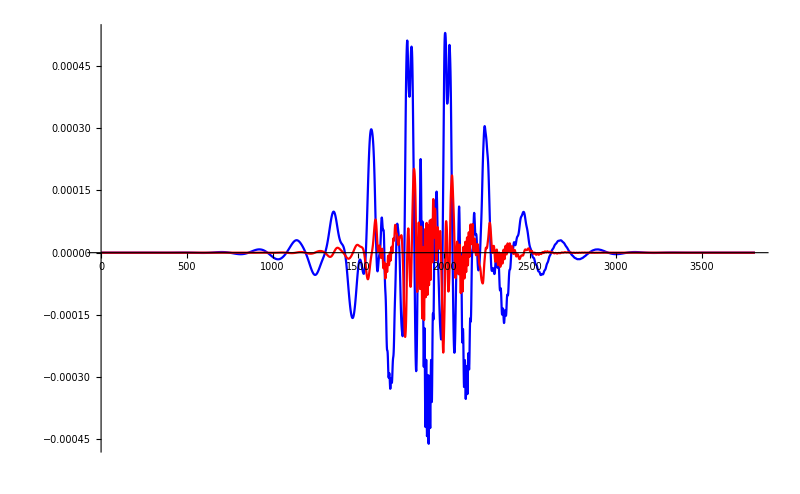

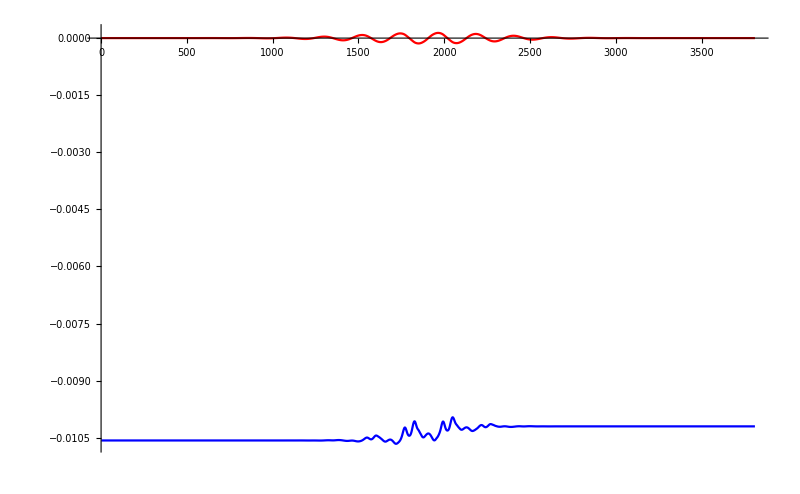

```mathematica
ListPlot[{xInterRad,yInterRad},PlotRange->All,Joined->True,PlotStyle->{Blue,Red},ImageSize->800]
ListPlot[{xIntraRad ,yIntraRad},PlotRange->All,Joined->True,PlotStyle->{Blue,Red},ImageSize->800]
```

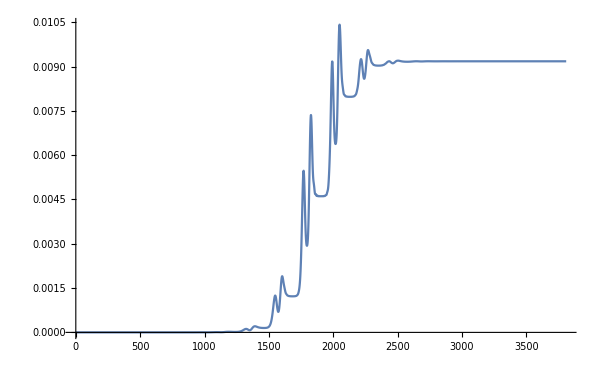

```mathematica
ListLinePlot[nc1[[1,All]],PlotRange->All,ImageSize->600]
```

```mathematica
xInterRad[[1]]



O1[kx_]:= cBerryCurvature[kx,0,t01,t02,M0,phi0,aax,aay,bbx,bby]
```

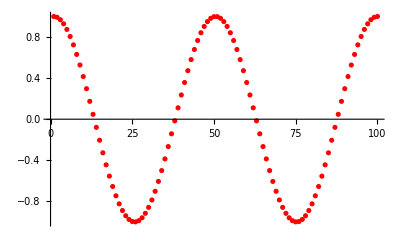

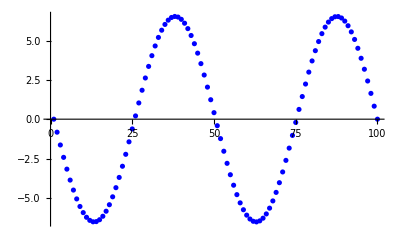

```mathematica
FirstDerOperator := Function [
{dx,Nx},

Mtemp=SparseArray[{Band[{1,1}]->0,Band[{2,1}]->-1,Band[{1,2}]->1},{Nx,Nx}]/2/dx;
Mtemp[[1]][[Nx-1]]=-1/dx/2.;
Mtemp[[1]][[1]]=-0/dx/2;
Mtemp[[Nx]][[Nx]]=0/dx/2;
Mtemp[[Nx]][[2]]=1/dx/2.;
Mtemp

];


Nx=100;
dkx=2 kxMax/(Nx-1);
reg0=0;
y = Table[
tkx= kxMin  + i dkx;
Cos[tkx 2 Pi/( kxMax)]
(*Re[cBerryCurvature[tkx,0,t01,t02,M0,phi0,aax,aay,bbx,bby]]*)
,{i,0,Nx-1}
];

Dx = FirstDerOperator[dkx,Nx];
Dy = Dx.y;

ListPlot[y,PlotRange->All,PlotStyle->Red]
ListPlot[Dy,PlotRange->All,PlotStyle->Blue]
```

```mathematica
EfieldA[t_]:= E0 Cos[t w0/cycles0/2 ] Cos[t w0/cycles0/2 ] Cos[ w0 t -cep0];
AfieldA[t_]:=-Integrate[EfieldA[ta],ta]/.ta-> t;

AfieldB[t_]:= -E0/w0 Cos[t w0/cycles0/2 ] Cos[t w0/cycles0/2 ] Sin[ w0 t -cep0];
EfieldB[t_]:= -D[AfieldB[ta],ta]/.ta-> t;
```

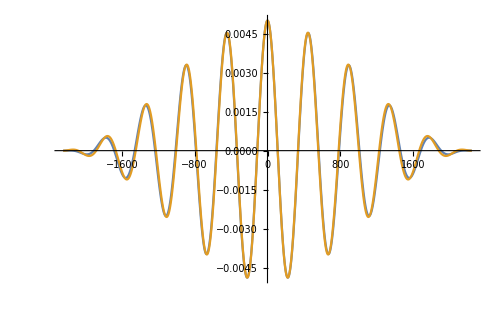

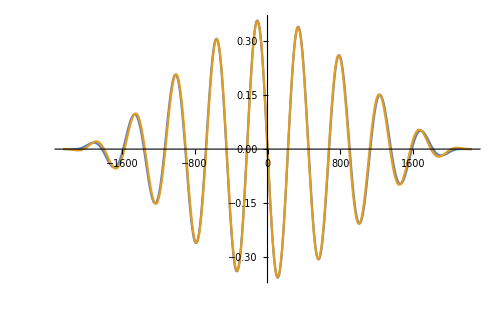

```mathematica
E0=0.005;
w0=0.014;
T0= 2 π/w0;
cycles0=10;
width0= cycles0 T0;
cep0=0;
Plot[{EfieldA[t],EfieldB[t]},{t,-width0/2,width0/2},PlotRange->All,ImageSize->500] 
Plot[{AfieldA[t], AfieldB[t]},{t,-width0/2,width0/2},PlotRange->All,ImageSize->500]
```

```mathematica
CForm[f]
```

(2*(-1 + Power(cycles0,2))*Sin(cep0 - t*w0) + cycles0*(1 + cycles0)*Sin(cep0 + (-1 + 1/cycles0)*t*w0) + 
     (-1 + cycles0)*cycles0*Sin(cep0 - ((1 + cycles0)*t*w0)/cycles0))/(4.*(-1 + cycles0)*(1 + cycles0)*w0)

```mathematica
Clear[s,w0,cep0,E0,width1];

$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`2"&);
xAf[t_] := E0/w0 Exp[ - (t/width1)^2/2] Cos[w0 t -cep0]; 
yAf[t_] := E0/w0 Exp[ - (t/width1)^2/2] Sin[w0 t -cep0]; 

xE:=Function[t,-D[xAf[ta],ta]/.ta-> t]
yE:=Function[t, -D[yAf[ta],ta]/.ta-> t]


xEfieldA[t_]:= E0 Exp[ - (t/width1)^2/2] Sin[w0 t -cep0];
xAfieldA[t_]:= -Integrate[xEfield[ta],ta]/.ta->t (*1/2 ⅇ^(-1/2 w0^2 width1^2) E0 √(π/2) width1* (Erfi[(ⅈ t+w0 width1^2)/(√2 width1)] (Cos[cep0]-ⅈ Sin[cep0])+Erfi[(-ⅈ t+w0 width1^2)/(√2 width1)] (Cos[cep0]+ⅈ Sin[cep0]))*);
```

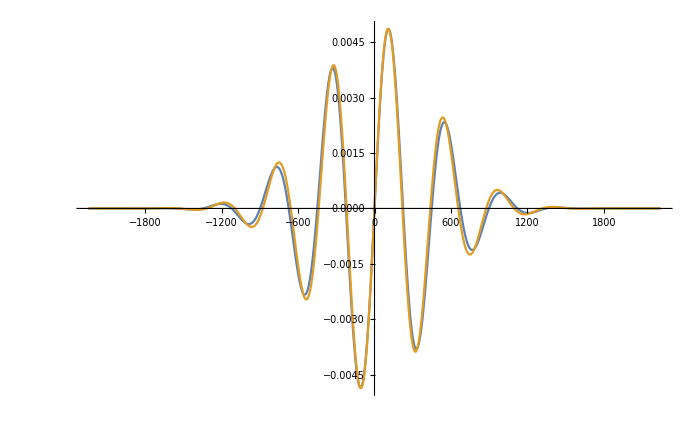

```mathematica
E0=0.005;
w0=0.014;
T0=2 Pi /w0;
cep0=0;
width1 =  1 T0;
Plot[{xEfieldA[t],xE[t]},{t,-5 width1 ,5 width1 },PlotRange->All,ImageSize->700]

Plot[{ Re[xAfieldA[t]],xAf[t]},{t,-5 width1 ,5 width1 },PlotRange->All,ImageSize->700]
```

```mathematica
x={1,2,3,4};
Sum[x[[i]],{i,1,4}]
```

10